# Symbolic computation for quantum states

Compute symbolic operations on quantum state

## Example Content

In Wolfram quantum framework, a quantum state can be defined symbolically. Therefore, its transformation due to, e.g., measurement, quantum channel, unitary transformation and more can be computed symbolically, too.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
QuantumOperator["H"]@QuantumState[{α,β}]//TraditionalForm
```

(α/(√2)+β/(√2)) 0+(α/(√2)-β/(√2)) 1

Generalized Pauli-X in 3D transforms a symbolic 3D quantum state:

```mathematica
QuantumOperator[{"X",3}][QuantumState[{α,β,γ},3]]//TraditionalForm
```

√2 β 0+(√2 α+√2 γ) 1+√2 β 2

Symbolic basis transformation:

```mathematica
ψ0=QuantumState[{x,y},QuantumBasis[<|0->{a,b},1->{c,d}|>]];
QuantumState[ψ0,"X"]//TraditionalForm
```

(-(a x+c y)/(√2)+(b x+d y)/(√2)) ψ_(x_-)+((a x+c y)/(√2)+(b x+d y)/(√2)) ψ_(x_+)

Symbolic computation of quantum measurement:

```mathematica
mea=QuantumMeasurementOperator[][QuantumState[{Cos[θ/2],ⅇ^(ⅈ ϕ)Sin[θ/2]}]]
```

QuantumMeasurement[…]

Measurement probabilities:

```mathematica
FullSimplify[#,Assumptions->{ϕ∈Reals,θ∈Reals}]&/@mea["Probabilities"]
```

<|0→Cos[θ/2]^2,1→Sin[θ/2]^2|>

Define a symbolic multiplexer circuit:

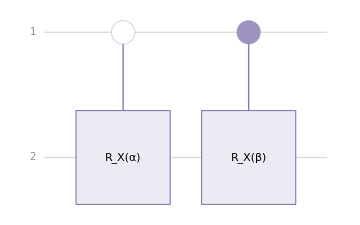

```mathematica
qc=QuantumCircuitOperator[{"Multiplexer",{"RX",α},{"RX",β}}];
qc["Diagram"]
```

Find the final state vector, after acting the above circuit on a symbolic 2-qubit state:

```mathematica
FullSimplify/@Normal[qc[QuantumState[{c1,c2,c3,c4}]]["StateVector"]]
```

{c1 Cos[α/2]-ⅈ c2 Sin[α/2],c2 Cos[α/2]-ⅈ c1 Sin[α/2],c3 Cos[β/2]-ⅈ c4 Sin[β/2],c4 Cos[β/2]-ⅈ c3 Sin[β/2]}

Given a symbolic quantum channel, transform a symbolic quantum state

```mathematica
ρ=QuantumChannel[{"BitFlip",p}][QuantumState[{Cos[θ/2],ⅇ^(ⅈ ϕ)Sin[θ/2]}]]
```

QuantumState[…]

Represent the final density matrix:

```mathematica
FullSimplify[#,Assumptions->{0<=p<=1,ϕ∈Reals,θ∈Reals}]&/@Normal[ρ["DensityMatrix"]]//MatrixForm
```

(1/2 (1+Cos[θ]-2 p Cos[θ]) | 1/2 Sin[θ] (Cos[ϕ]+ⅈ (-1+2 p) Sin[ϕ])
1/2 Sin[θ] (Cos[ϕ]+ⅈ (1-2 p) Sin[ϕ]) | 1/2 (1+(-1+2 p) Cos[θ]))

Evolve a symbolic quantum state by a symbolic Hamiltonian in time:

```mathematica
QuantumEvolve[QuantumOperator["X"],QuantumState[{α,β}],t]["StateVector"]//MatrixForm
```

(α Cos[t]-ⅈ β Sin[t]
β Cos[t]-ⅈ α Sin[t])

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

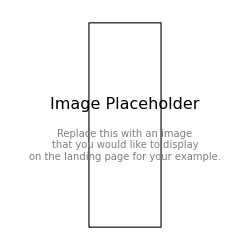

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum state

Symbolic computation

Quantum transformation

Quantum operation

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.